# Parcels

Gustavo Delfino, 2013-07-08

## The Excercise

This would be the exercise:

## Find the most efficient combination of 3kg and 5kg parcels required to make any shipment of 8kg or more. The app will accept input from a web form.

## Output should either be a simple result view or for bonus points, rendered on the same page via AJAX without page refresh. So given 11, output should be:

## 1 five kg parcels, 2 three kg parcels

## Input should be validated.

## Assume at least Ruby 1.9.3 and Rails 3+. Please use TDD and submit your answer with either a private github repo or via email.

## Manual Procedure

These are the manual operations that were made in order to think about a more general algorithm:

Suppose we want a 99kg shipment:

```mathematica
num=99
```

99

```mathematica
num/5.
```

19.8

```mathematica
Floor[num/5]
```

19

```mathematica
5Floor[num/5]
```

95

```mathematica
num-5Floor[num/5]
```

4

```mathematica
Divisible[num-5Floor[num/5],3]
```

False

Now try with one fewer 5kg parsel

```mathematica
Floor[num/5]-1
```

18

```mathematica
5(Floor[num/5]-1)
```

90

```mathematica
num-5(Floor[num/5]-1)
```

9

```mathematica
Divisible[num-5(Floor[num/5]-1),3]
```

True

Now calculate the number of required 3kg parsels:

```mathematica
(num-5(Floor[num/5]-1))/3
```

3

Verification:

```mathematica
18 5+3 3
```

99

## Automating the Search of a Solution

### Function to calculate the parsels

```mathematica
parsels[n_]:=NestWhile[{n-5(⌊n/5⌋-#⟦3⟧),5(⌊n/5⌋-#⟦3⟧),#⟦3⟧+1}&,{1,n,0},(!Divisible[#⟦1⟧,3])&]/.{iii_,v_,_}:>{v/5,iii/3}
```

```mathematica
parsels[99]
```

{18,3}

### Function to pretty print the parsels

```mathematica
printParsels[{0,iii_}]:=Row[{3,"×",iii}]
```

```mathematica
printParsels[{v_,0}]:=Row[{5,"×",v}]
```

```mathematica
printParsels[{v_,iii_}]:=Row[{5,"×",v," + ",3,"×",iii}]
```

```mathematica
printParsels[parsels[99]]
```

5×18+3×3

### Table of Results

```mathematica
Table[{n,printParsels[parsels[n]]},{n,8,100}]//TableForm
```

8 | 5×1 + 3×1
9 | 3×3
10 | 5×2
11 | 5×1 + 3×2
12 | 3×4
13 | 5×2 + 3×1
14 | 5×1 + 3×3
15 | 5×3
16 | 5×2 + 3×2
17 | 5×1 + 3×4
18 | 5×3 + 3×1
19 | 5×2 + 3×3
20 | 5×4
21 | 5×3 + 3×2
22 | 5×2 + 3×4
23 | 5×4 + 3×1
24 | 5×3 + 3×3
25 | 5×5
26 | 5×4 + 3×2
27 | 5×3 + 3×4
28 | 5×5 + 3×1
29 | 5×4 + 3×3
30 | 5×6
31 | 5×5 + 3×2
32 | 5×4 + 3×4
33 | 5×6 + 3×1
34 | 5×5 + 3×3
35 | 5×7
36 | 5×6 + 3×2
37 | 5×5 + 3×4
38 | 5×7 + 3×1
39 | 5×6 + 3×3
40 | 5×8
41 | 5×7 + 3×2
42 | 5×6 + 3×4
43 | 5×8 + 3×1
44 | 5×7 + 3×3
45 | 5×9
46 | 5×8 + 3×2
47 | 5×7 + 3×4
48 | 5×9 + 3×1
49 | 5×8 + 3×3
50 | 5×10
51 | 5×9 + 3×2
52 | 5×8 + 3×4
53 | 5×10 + 3×1
54 | 5×9 + 3×3
55 | 5×11
56 | 5×10 + 3×2
57 | 5×9 + 3×4
58 | 5×11 + 3×1
59 | 5×10 + 3×3
60 | 5×12
61 | 5×11 + 3×2
62 | 5×10 + 3×4
63 | 5×12 + 3×1
64 | 5×11 + 3×3
65 | 5×13
66 | 5×12 + 3×2
67 | 5×11 + 3×4
68 | 5×13 + 3×1
69 | 5×12 + 3×3
70 | 5×14
71 | 5×13 + 3×2
72 | 5×12 + 3×4
73 | 5×14 + 3×1
74 | 5×13 + 3×3
75 | 5×15
76 | 5×14 + 3×2
77 | 5×13 + 3×4
78 | 5×15 + 3×1
79 | 5×14 + 3×3
80 | 5×16
81 | 5×15 + 3×2
82 | 5×14 + 3×4
83 | 5×16 + 3×1
84 | 5×15 + 3×3
85 | 5×17
86 | 5×16 + 3×2
87 | 5×15 + 3×4
88 | 5×17 + 3×1
89 | 5×16 + 3×3
90 | 5×18
91 | 5×17 + 3×2
92 | 5×16 + 3×4
93 | 5×18 + 3×1
94 | 5×17 + 3×3
95 | 5×19
96 | 5×18 + 3×2
97 | 5×17 + 3×4
98 | 5×19 + 3×1
99 | 5×18 + 3×3
100 | 5×20

### 10000 Tests !

Test from 8kg to 10000kg

```mathematica
And@@Table[n==5parsels[n]⟦1⟧+3parsels[n]⟦2⟧,{n,8,10000}]
```

True

### Plots

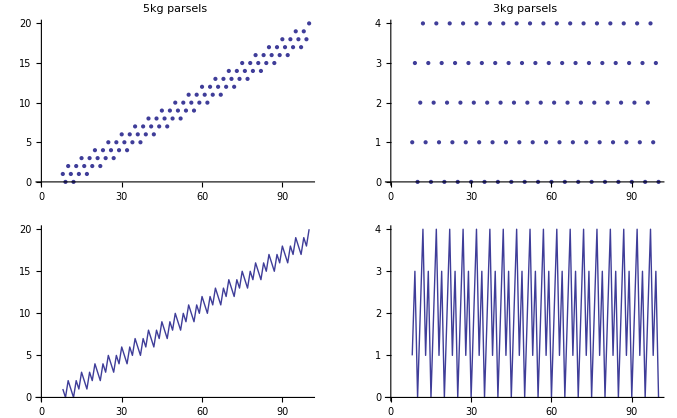

```mathematica
GraphicsGrid[
{{ListPlot[{Table[{n,parsels[n][[1]]},{n,8,100}]},PlotLabel->"5kg parsels"],
ListPlot[{Table[{n,parsels[n][[2]]},{n,8,100}]},PlotLabel->"3kg parsels"]},
{ListPlot[{Table[{n,parsels[n][[1]]},{n,8,100}]},Joined->True],
ListPlot[{Table[{n,parsels[n][[2]]},{n,8,100}]},Joined->True]}}]
```

## Iteration Free Algorithm

### 3kg Units

These are the first few terms of the 3kg sequence:

```mathematica
Table[parsels[n]⟦2⟧,{n,8,20}]
```

{1,3,0,2,4,1,3,0,2,4,1,3,0}

Mathematica finds the generating function directly!

```mathematica
FindSequenceFunction[%]
```

Mod[4+2 #1,5]&

As a verification we will plot this function over the original function with an offset of 1:

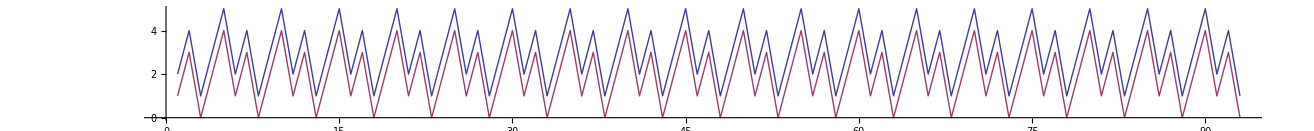

```mathematica
ListPlot[
{Table[parsels[n][[2]]+1,{n,8,100}],
Table[Mod[2#-10,5]&[n],{n,8,100}]},Joined->True,AspectRatio->1/10]
```

### 5kg Units

These are the first few terms of the 5kg sequence:

```mathematica
Table[parsels[n]⟦1⟧,{n,8,20}]
```

{1,0,2,1,0,2,1,3,2,1,3,2,4}

This time we are not so lucky as Mathematica can’t find a simple closed for solution for our sequence. But we can with a little work.

```mathematica
FindSequenceFunction[%]
```

DifferenceRoot[Function[{y,n},{-1-y[n]+y[5+n]==0,y[1]==1,y[2]==0,y[3]==2,y[4]==1,y[5]==0}]]

Lets remove the slope from this sequence by substracting n/5 from it:

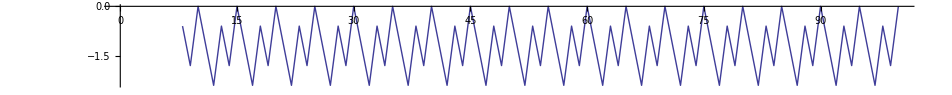

```mathematica
ListPlot[Table[{n,parsels[n]⟦1⟧-n/5},{n,8,100}],Joined->True,AspectRatio->1/10]
```

```mathematica
Table[parsels[n]⟦1⟧-n/5,{n,8,50}]
```

{-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0}

Mathematica now can find the generating function, but it is too complicated...

```mathematica
FindSequenceFunction[%]//Simplify
```

-6/5-12/25 Cos[2/5 π (-5+#1)]-12/25 Cos[4/5 π (-5+#1)]-12/25 Cos[6/5 π (-5+#1)]-12/25 Cos[8/5 π (-5+#1)]-6/25 Cos[2/5 π (-4+#1)]-6/25 Cos[4/5 π (-4+#1)]-6/25 Cos[6/5 π (-4+#1)]-6/25 Cos[8/5 π (-4+#1)]-9/25 Cos[2/5 π (-2+#1)]-9/25 Cos[4/5 π (-2+#1)]-9/25 Cos[6/5 π (-2+#1)]-9/25 Cos[8/5 π (-2+#1)]-3/25 Cos[2/5 π (-1+#1)]-3/25 Cos[4/5 π (-1+#1)]-3/25 Cos[6/5 π (-1+#1)]-3/25 Cos[8/5 π (-1+#1)]&

The linearized sequence is greatly simplified by multiplicating it by 5:

```mathematica
5Table[parsels[n]⟦1⟧-n/5,{n,8,50}]
```

{-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0}

And this is just a repeating pattern:

```mathematica
Table[First[RotateLeft[{-3,-9,0,-6,-12},n-8]],{n,8,50}]
```

{-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0,-6,-12,-3,-9,0}

Reversing the transformations:

```mathematica
Table[First[RotateLeft[{-3,-9,0,-6,-12},n-8]]/5,{n,8,50}]
```

{-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0,-6/5,-12/5,-3/5,-9/5,0}

```mathematica
Table[(First[RotateLeft[{-3,-9,0,-6,-12},n-8]]+n)/5,{n,8,50}]
```

{1,0,2,1,0,2,1,3,2,1,3,2,4,3,2,4,3,5,4,3,5,4,6,5,4,6,5,7,6,5,7,6,8,7,6,8,7,9,8,7,9,8,10}

And this matches the original iterative function:

```mathematica
Table[parsels[n]⟦1⟧,{n,8,50}]
```

{1,0,2,1,0,2,1,3,2,1,3,2,4,3,2,4,3,5,4,3,5,4,6,5,4,6,5,7,6,5,7,6,8,7,6,8,7,9,8,7,9,8,10}

## Combinations

```mathematica
d=Flatten[Table[{a,b,3a+5b},{a,1,5,1/10},{b,1,5,1/10}],1];
```

```mathematica
Cases[d,{_Rational,_Rational,_Integer}]
```

{{3/2,11/10,10},{3/2,13/10,11},{3/2,3/2,12},{3/2,17/10,13},{3/2,19/10,14},{3/2,21/10,15},{3/2,23/10,16},{3/2,5/2,17},{3/2,27/10,18},{3/2,29/10,19},{3/2,31/10,20},{3/2,33/10,21},{3/2,7/2,22},{3/2,37/10,23},{3/2,39/10,24},{3/2,41/10,25},{3/2,43/10,26},{3/2,9/2,27},{3/2,47/10,28},{3/2,49/10,29},{5/2,11/10,13},{5/2,13/10,14},{5/2,3/2,15},{5/2,17/10,16},{5/2,19/10,17},{5/2,21/10,18},{5/2,23/10,19},{5/2,5/2,20},{5/2,27/10,21},{5/2,29/10,22},{5/2,31/10,23},{5/2,33/10,24},{5/2,7/2,25},{5/2,37/10,26},{5/2,39/10,27},{5/2,41/10,28},{5/2,43/10,29},{5/2,9/2,30},{5/2,47/10,31},{5/2,49/10,32},{7/2,11/10,16},{7/2,13/10,17},{7/2,3/2,18},{7/2,17/10,19},{7/2,19/10,20},{7/2,21/10,21},{7/2,23/10,22},{7/2,5/2,23},{7/2,27/10,24},{7/2,29/10,25},{7/2,31/10,26},{7/2,33/10,27},{7/2,7/2,28},{7/2,37/10,29},{7/2,39/10,30},{7/2,41/10,31},{7/2,43/10,32},{7/2,9/2,33},{7/2,47/10,34},{7/2,49/10,35},{9/2,11/10,19},{9/2,13/10,20},{9/2,3/2,21},{9/2,17/10,22},{9/2,19/10,23},{9/2,21/10,24},{9/2,23/10,25},{9/2,5/2,26},{9/2,27/10,27},{9/2,29/10,28},{9/2,31/10,29},{9/2,33/10,30},{9/2,7/2,31},{9/2,37/10,32},{9/2,39/10,33},{9/2,41/10,34},{9/2,43/10,35},{9/2,9/2,36},{9/2,47/10,37},{9/2,49/10,38}}

## Data for Ruby Test

```mathematica
CopyToClipboard[ExportString[Table[Join[{kg},parsels[kg]],{kg,8,100,1}],"CSV"]]
```

## Decor

```mathematica
g1=Column[Grid[{#},Spacings->0]&/@Table[parsels[n],{n,8,40}]/.{v_,iii_}:>Flatten[{Table[5,{v}],Table[3,{iii}]}]/.
{5->Graphics[{Lighter[Red],Rectangle[{0,0},{5,3}]},ImageSize->{50,30}],
3->Graphics[{Lighter[Blue],Rectangle[{0,0},{3,3}]},ImageSize->{30,30}]},Alignment->Right,Spacings->0]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
g2=ImageReflect[Rasterize[Rotate[g1,π/2],Background->None]]
```

-Graphics-

```mathematica
Export["~/Sites/parsels/app/assets/images/bg.png",g2,Background->None]
```

~/Sites/parsels/app/assets/images/bg.png